## First - two masses and three strings

```mathematica
l1 = 1;
l12 = 2;
l2 = l1 + l12;
k =1;
```

```mathematica
solution = Simplify@DSolve[{
x1''[t] == -k(x1[t] -l1) + k(x2[t]-x1[t]-l12),
x2''[t] == -k(x2[t] - l2) + k(x1[t] - x2[t] + l12),
x1[0] == 1,
x1'[0] == 0,
x2[0] == 2.7,
x2'[0] == 0
},
{x1[t], x2[t]}, t
]
```

{{x1[t]→ⅇ^(-2 ⅈ (1+√3) √k t) (ⅇ^(ⅈ (1+2 √3) √k t) (0.925-0.25 l1-0.25 l2)+ⅇ^(ⅈ (3+2 √3) √k t) (0.925-0.25 l1-0.25 l2)+ⅇ^(ⅈ (2+√3) √k t) (-0.425-0.0833333 l1+0.166667 l12+0.0833333 l2)+ⅇ^(ⅈ (2+3 √3) √k t) (-0.425-0.0833333 l1+0.166667 l12+0.0833333 l2)+ⅇ^(2 ⅈ (1+√3) √k t) (0.666667 l1-0.333333 l12+0.333333 l2)),x2[t]→ⅇ^(-2 ⅈ (1+√3) √k t) (ⅇ^(ⅈ (1+2 √3) √k t) (0.925-0.25 l1-0.25 l2)+ⅇ^(ⅈ (3+2 √3) √k t) (0.925-0.25 l1-0.25 l2)+ⅇ^(ⅈ (2+√3) √k t) (0.425+0.0833333 l1-0.166667 l12-0.0833333 l2)+ⅇ^(ⅈ (2+3 √3) √k t) (0.425+0.0833333 l1-0.166667 l12-0.0833333 l2)+ⅇ^(2 ⅈ (1+√3) √k t) (0.333333 l1+0.333333 l12+0.666667 l2))}}

```mathematica
2
```

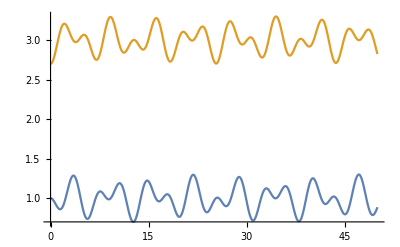

```mathematica
Plot[{solution[[1,1, 2]], solution[[1,2, 2]]}, {t, 0, 50}]
```